```mathematica
Integrate[Exp[I k x],x]
```

-(ⅈ ⅇ^(ⅈ k x))/k

```mathematica
Integrate[Exp[(I x-α) k ]/k,{k,ϵ,Infinity}]
```

ConditionalExpression[Gamma[0,(-ⅈ x+α) ϵ], Re[ϵ]>0&&Im[ϵ]==0&&Im[x]+Re[α]>0]

```mathematica
Simplify[Integrate[Exp[(I x-α) k ]/k,{k,ϵ,Infinity}],Assumptions->{ϵ>0,α>0,Im[x]==0}]
```

Gamma[0,(-ⅈ x+α) ϵ]

```mathematica
Simplify[Gamma[0,(-ⅈ x+α) ϵ]+Gamma[0,(ⅈ x+α) ϵ]]
```

Gamma[0,(-ⅈ x+α) ϵ]+Gamma[0,(ⅈ x+α) ϵ]

```mathematica
?Series
```

```mathematica
Series[Gamma[0,-I x]+Gamma[0,I x],{x,0,3}]
```

-2 ⅈ π Floor[(π/2-Arg[x])/(2 π)]-2 ⅈ π Floor[((3 π)/2-Arg[x])/(2 π)]+(-2 (EulerGamma+Log[x])+x^2/2+O[x]^4)

```mathematica
-2 ⅈ π Floor[(π/2)/(2 π)]-2 ⅈ π Floor[((3 π)/2)/(2 π)]
```

0

```mathematica
Arg[3]
```

0

```mathematica
Re[Gamma[0,0]+Gamma[0,0]]
```

∞

```mathematica
N[EulerGamma]
```

0.577216

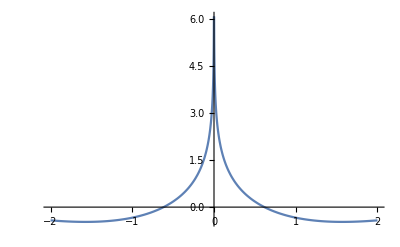

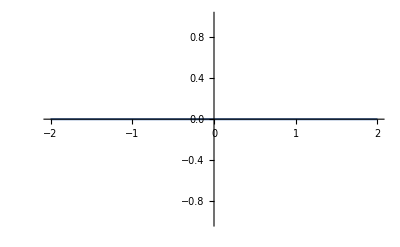

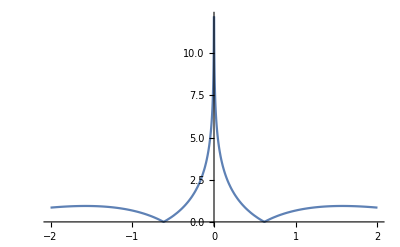

```mathematica
r=2;
Plot[Re[Gamma[0,I x]],{x,-r,r},PlotRange->All]
Plot[Im[Gamma[0,-I x]+Gamma[0,I x]],{x,-r,r},PlotRange->All]
Plot[Abs[Gamma[0,-I x]+Gamma[0,I x]],{x,-r,r},PlotRange->All]
```